-Graphics-
Image source: How does Effervescent Tablet dissolve in water

# Physical Chemistry

## Experimental Design, Nonlinear Fitting, Model Selection, Machine Learning

Jozsef Konczer

@ Milestone Institute

## Questions:

How fast of an effervescent vitamin tablet dissolves in a glass of water on different temperature?

What could be the relevant Parameters?

How reliable the dependence is?

## Experimental Game

## First choose 3 Data Points

```mathematica
temperatureOptions={{1,5},{2,16},{3,19},{4,23},{5,25},{6,25},{7,35},{8,38},{9,47},{10,60},{11,63},{12,72},{13,100},{14,100}};
```

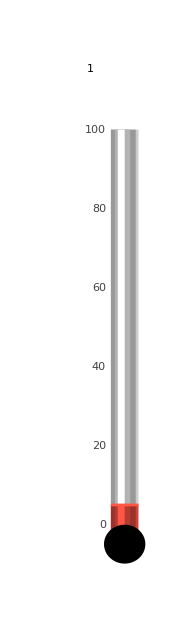
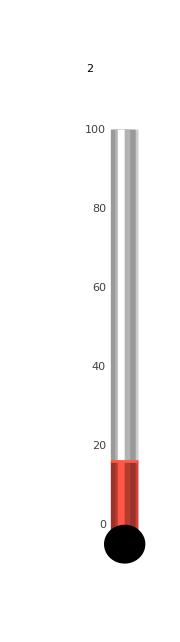
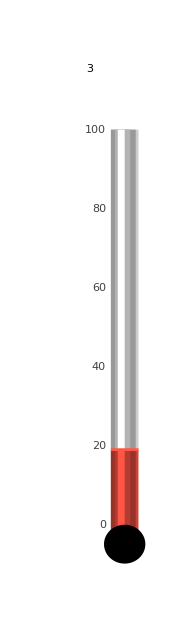
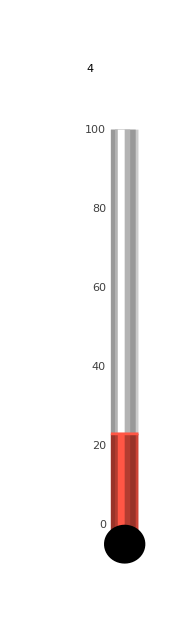
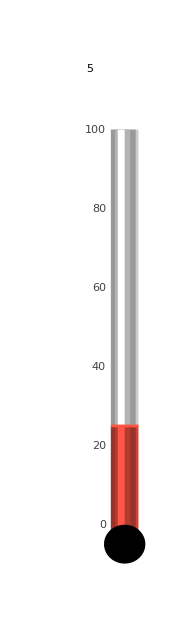
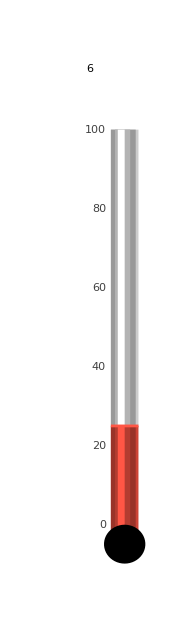
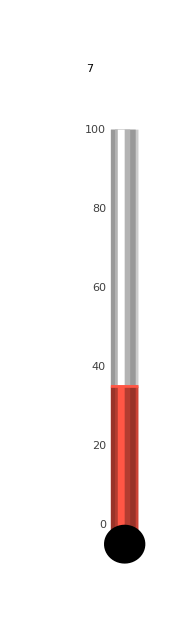
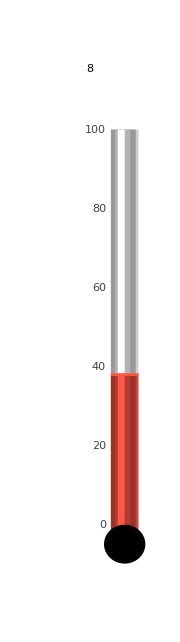

```mathematica
Show[ThermometerGauge[#[[2]],{0,100}],PlotLabel->Style[#[[1]],Bold,FontSize->14]]&/@temperatureOptions
```

```mathematica
(*Password: "ExperimentalGame"*)
firstChoice={□,□,□}
data1=Check[({#["WaterTemperature"],{60,1}.#["TimeOfDissolution"][[1]]}&/@SortBy[Decrypt[EncryptedObject[…]],#["WaterTemperature"]&])[[firstChoice[[;;3]]]],$Failed]
```

```mathematica
ListLinePlot[Sort[data1],AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]
```

#### Original parameters (Time - Temperature in °C)

```mathematica
With[
{nlm=NonlinearModelFit[data1,a+b t,{a,b},t]},
Print["Time = ",nlm["BestFit"]];
Print["Bayesian information criterion: ",nlm["BIC"]];
Show[ListPlot[data1],Plot[nlm["BestFit"],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data1],Plot[nlm["BestFit"],{t,0,100}],Plot[Evaluate[nlm["MeanPredictionBands",ConfidenceLevel->.95]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

```mathematica
With[
{nlm=NonlinearModelFit[data1,a t^b,{a,b},t]},
Print["Time = ",nlm["BestFit"]];
Print["Bayesian information criterion: ",nlm["BIC"]];
Show[ListPlot[data1],Plot[nlm["BestFit"],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data1],Plot[nlm["BestFit"],{t,0,100}],Plot[Evaluate[nlm["MeanPredictionBands",ConfidenceLevel->.95]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

```mathematica
With[
{nlm=NonlinearModelFit[data1,a Exp[-b t],{a,b},t]},
Print["Time = ",nlm["BestFit"]];
Print["Bayesian information criterion: ",nlm["BIC"]];
Show[ListPlot[data1],Plot[nlm["BestFit"],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data1],Plot[nlm["BestFit"],{t,0,100}],Plot[Evaluate[nlm["MeanPredictionBands",ConfidenceLevel->.95]],{t,0,100},Filling->{1->{2}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large],PlotRange->{{0,100},{0,All}}]//Print
]
```

```mathematica
With[
{nlm=NonlinearModelFit[data1,a Exp[-b /(273+t)],{a,b},t]},
Print["Time = ",nlm["BestFit"]];
Print["Bayesian information criterion: ",nlm["BIC"]];
Show[ListPlot[data1],Plot[nlm["BestFit"],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data1],Plot[nlm["BestFit"],{t,0,100}],Plot[Evaluate[nlm["MeanPredictionBands",ConfidenceLevel->.95]],{t,0,100},Filling->{1->{2}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

#### Transformed parameters (Log(Time/(60 s)) - Absolute Temperature in 1000 K)

```mathematica
data1TLog={(#[[1]]+273)/1000,Log[#[[2]]/60.]}&/@data1;
With[
{nlmTLog=NonlinearModelFit[data1TLog,a+b Tn,{a,b},Tn]},
Print["Log[Time/(60 s)] = ",nlmTLog["BestFit"]];
Print["Bayesian information criterion: ",nlmTLog["BIC"]];
Show[ListPlot[data1],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data1],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],Plot[Evaluate[60Exp[nlmTLog["MeanPredictionBands",ConfidenceLevel->.95]/.Tn->(t+273)/1000.]],{t,0,100},Filling->{1->{2}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large],PlotRange->{{0,100},{0,All}}]//Print
]
```

```mathematica
data1TLog={(#[[1]]+273)/1000,Log[#[[2]]/60.]}&/@data1;
With[
{nlmTLog=NonlinearModelFit[data1TLog,a+b/ Tn,{a,b},Tn]},
Print["Log[Time/(60 s)] = ",nlmTLog["BestFit"]];
Print["Bayesian information criterion: ",nlmTLog["BIC"]];
Show[ListPlot[data1],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data1],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],Plot[Evaluate[60Exp[nlmTLog["MeanPredictionBands",ConfidenceLevel->.95]/.Tn->(t+273)/1000]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

```mathematica
data1TLog={(#[[1]]+273)/1000,Log[#[[2]]/60.]}&/@data1;
With[
{nlmTLog=NonlinearModelFit[data1TLog,a+b/ (Tn)^c,{a,b,c},Tn]},
Print["Log[Time/(60 s)] = ",nlmTLog["BestFit"]];
Print["Bayesian information criterion: ",nlmTLog["BIC"]];
Show[ListPlot[data1],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data1],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],Plot[Evaluate[60Exp[nlmTLog["MeanPredictionBands",ConfidenceLevel->.95]/.Tn->(t+273)/1000]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

## Select 2 more Data points

```mathematica
temperatureOptions={{1,5},{2,16},{3,19},{4,23},{5,25},{6,25},{7,35},{8,38},{9,47},{10,60},{11,63},{12,72},{13,100},{14,100}};
```

```mathematica
Show[ThermometerGauge[#[[2]],{0,100}],PlotLabel->Style[#[[1]],Bold,FontSize->14]]&/@temperatureOptions
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Password: "ExperimentalGame"*)
secondChoice={□,□}
data2=Check[({#["WaterTemperature"],{60,1}.#["TimeOfDissolution"][[1]]}&/@SortBy[Decrypt[EncryptedObject[…]],#["WaterTemperature"]&])[[Join[firstChoice[[;;3]],secondChoice[[;;2]]]]],$Failed]
```

```mathematica
ListLinePlot[Sort[data2],AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]
```

#### Original parameters (Time - Temperature in °C)

```mathematica
With[
{nlm=NonlinearModelFit[data2,a+b t,{a,b},t]},
Print["Time = ",nlm["BestFit"]];
Print["Bayesian information criterion: ",nlm["BIC"]];
Show[ListPlot[data2],Plot[nlm["BestFit"],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data2],Plot[nlm["BestFit"],{t,0,100}],Plot[Evaluate[nlm["MeanPredictionBands",ConfidenceLevel->.95]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

```mathematica
With[
{nlm=NonlinearModelFit[data2,a t^b,{a,b},t]},
Print["Time = ",nlm["BestFit"]];
Print["Bayesian information criterion: ",nlm["BIC"]];
Show[ListPlot[data2],Plot[nlm["BestFit"],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data2],Plot[nlm["BestFit"],{t,0,100}],Plot[Evaluate[nlm["MeanPredictionBands",ConfidenceLevel->.95]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

```mathematica
With[
{nlm=NonlinearModelFit[data2,a Exp[-b t],{a,b},t]},
Print["Time = ",nlm["BestFit"]];
Print["Bayesian information criterion: ",nlm["BIC"]];
Show[ListPlot[data2],Plot[nlm["BestFit"],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data2],Plot[nlm["BestFit"],{t,0,100}],Plot[Evaluate[nlm["MeanPredictionBands",ConfidenceLevel->.95]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

```mathematica
With[
{nlm=NonlinearModelFit[data2,a Exp[-b /(273+t)],{a,b},t]},
Print["Time = ",nlm["BestFit"]];
Print["Bayesian information criterion: ",nlm["BIC"]];
Show[ListPlot[data2],Plot[nlm["BestFit"],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data2],Plot[nlm["BestFit"],{t,0,100}],Plot[Evaluate[nlm["MeanPredictionBands",ConfidenceLevel->.95]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

#### Transformed parameters (Log(Time/(60 s)) - Absolute Temperature in 1000 K)

```mathematica
data2TLog={(#[[1]]+273)/1000,Log[#[[2]]/60.]}&/@data2;
With[
{nlmTLog=NonlinearModelFit[data2TLog,a+b Tn,{a,b},Tn]},
Print["Log[Time/(60 s)] = ",nlmTLog["BestFit"]];
Print["Bayesian information criterion: ",nlmTLog["BIC"]];
Show[ListPlot[data2],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data2],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],Plot[Evaluate[60Exp[nlmTLog["MeanPredictionBands",ConfidenceLevel->.95]/.Tn->(t+273)/1000]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

```mathematica
data2TLog={(#[[1]]+273)/1000,Log[#[[2]]/60.]}&/@data2;
With[
{nlmTLog=NonlinearModelFit[data2TLog,a+b /Tn,{a,b},Tn]},
Print["Log[Time/(60 s)] = ",nlmTLog["BestFit"]];
Print["Bayesian information criterion: ",nlmTLog["BIC"]];
Show[ListPlot[data2],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data2],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],Plot[Evaluate[60Exp[nlmTLog["MeanPredictionBands",ConfidenceLevel->.95]/.Tn->(t+273)/1000]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

```mathematica
data2TLog={(#[[1]]+273)/1000,Log[#[[2]]/60.]}&/@data2;
With[
{nlmTLog=NonlinearModelFit[data2TLog,a+b /(Tn)^c,{a,b,c},Tn]},
Print["Log[Time/(60 s)] = ",nlmTLog["BestFit"]];
Print["Bayesian information criterion: ",nlmTLog["BIC"]];
Show[ListPlot[data2],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print;
Show[ListPlot[data2],Plot[60Exp[nlmTLog["BestFit"]/.Tn->(t+273)/1000],{t,0,100}],Plot[Evaluate[60Exp[nlmTLog["MeanPredictionBands",ConfidenceLevel->.95]/.Tn->(t+273)/1000]],{t,0,100},Filling->{1->{2}}],PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]//Print
]
```

#### Original parameters Machine Learning algorithms

```mathematica
trainingset=Rule@@#&/@data2
p=Predict[trainingset,Method->"NeuralNetwork"]
```

```mathematica
Show[Plot[{p[x],
p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},
{x,0,100},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},
Exclusions->False,
PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"},PlotRange->{{0,100},{0,All}}],ListPlot[List@@@data2,PlotStyle->Red,PlotLegends->{"Data"}],
PlotRange->{{0,100},{0,All}},AxesLabel->{"Temperature[°C]","Time[s]"},ImageSize->Large]
```

## Your Predictions:

Manual Input:

```mathematica
prediction={{5,□},{16,□},{19,□},{23,□},{25,□},{25,□},{35,□},{38,□},{47,□},{60,□},{63,□},{72,□},{100,□},{100,□}}
```

Formula based input:

```mathematica
temperatureOptions={{1,5},{2,16},{3,19},{4,23},{5,25},{6,25},{7,35},{8,38},{9,47},{10,60},{11,63},{12,72},{13,100},{14,100}};
prediction=Table[
{k,
With[{t=temperatureOptions[[k,2]]},
1/t]
},
{k,1,Length[temperatureOptions]}]
```

## Full Data Set

```mathematica
(*Password: "ExperimentalGame"*)
rawData=Decrypt[EncryptedObject[…]];
```

```mathematica
Dataset[rawData]
```

```mathematica
data=({#["WaterTemperature"],{60,1}.#["TimeOfDissolution"][[1]]}&/@SortBy[rawData,#["WaterTemperature"]&])
ListPlot[data]
```

```mathematica
gameScore=N[Total[((Last/@data)-(Last/@prediction))^2]/Length[data]];
Print["Your Score is: ",gameScore]
Show[
ListPlot[prediction],
ListPlot[data,PlotStyle->Black]
]
```

## Export to CSV

```mathematica
rawData2=Association@@#&/@Normal/@(rawData/.{DateObject[x__]:>TextString[DateObject[x],DateFormat->{"Year","-","Month","-","Day", " ", "Hour",":","Minute"}],TimeObject[x__]:>TextString[TimeObject[x]],GeoPosition[x__]:>TextString[x,ListFormat->{"",", ",""}],{Entity[x__],y__}:>TextString[{TextString[Entity[x]],TextString[y]},ListFormat->{"",", ",""}]});
```

```mathematica
Export[NotebookDirectory[]<>"/RawData.csv",Dataset[rawData2]]
```

/home/josi/Work/Milestone/DataScience/03_PhysicalChemistry//RawData.csv

## Calculation:

Live Coding

## References:

Arrhenius equation

https://en.wikipedia.org/wiki/Arrhenius_equation

https://www.ncbi.nlm.nih.gov/pmc/articles/PMC8658926/

Model Selection

https://en.wikipedia.org/wiki/Model_selection